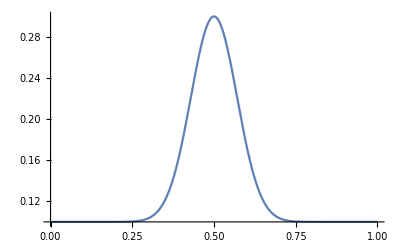

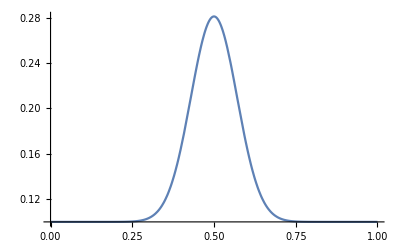

```mathematica
t0 = 0;
t1 = 0.1;
q[t_,x_]:=2/10*E^(-100t)*E^(-100(x-1/2)^2)+1/10
Plot[q[t0,x],{x,0,1},PlotRange->All]
Plot[q[t1,x],{x,0,1},PlotRange->All]
(*D[q[t,x],t]+D[q[t,x]^2-q[t,x]^3,x]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//FullSimplify
D[q[t,x],t]+D[q[t,x]^2-q[t,x]^3,x]//FullSimplify*)
```

```mathematica
D[q[t,x],t]
```

0

```mathematica
q[t,x]^3
```

(1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^3

```mathematica
D[q[t,x],{x,3}]
```

1/5 (120000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)-8000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^3)

```mathematica
D[q[t,x]^3 D[q[t,x],{x,3}],x]
```

1/5 (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^3 (120000 ⅇ^(-100 (-1/2+x)^2)-48000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^2+1600000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^4)-24 ⅇ^(-100 (-1/2+x)^2) (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^2 (120000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)-8000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^3) (-1/2+x)

```mathematica
D[q[t,x],t]+D[q[t,x]^3 D[q[t,x],{x,3}],x]
```

1/5 (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^3 (120000 ⅇ^(-100 (-1/2+x)^2)-48000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^2+1600000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^4)-24 ⅇ^(-100 (-1/2+x)^2) (1/10+1/5 ⅇ^(-100 (-1/2+x)^2))^2 (120000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)-8000000 ⅇ^(-100 (-1/2+x)^2) (-1/2+x)^3) (-1/2+x)

```mathematica
D[q[t,x],t]+D[q[t,x]^3 D[q[t,x],{x,3}],x]//Simplify
```

8 ⅇ^(-100 (1-2 x)^2) (2+ⅇ^(25 (1-2 x)^2))^2 (ⅇ^(25 (1-2 x)^2) (2203-18800 x+58800 x^2-80000 x^3+40000 x^4)+2 (9253-77000 x+237000 x^2-320000 x^3+160000 x^4))

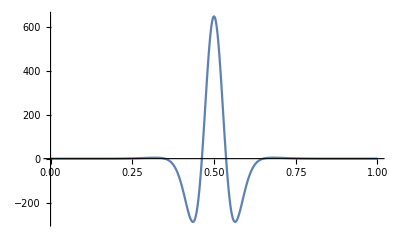

```mathematica
Plot[8 ⅇ^(-100 (1-2 x)^2) (2+ⅇ^(25 (1-2 x)^2))^2 (ⅇ^(25 (1-2 x)^2) (2203-18800 x+58800 x^2-80000 x^3+40000 x^4)+2 (9253-77000 x+237000 x^2-320000 x^3+160000 x^4)),{x,0,1},PlotRange->All]
```

```mathematica
NDSolve[{D[u[t,x],t]+D[u[t,x]^2-u[t,x]^3,x]==-27/10 ⅇ^(-225 (1-2 x)^2) (-9+20 ⅇ^(75 (1-2 x)^2)) (-1+2 x),u[0,x]==3/10*E^(-300(x-1/2)^2),u[t,0]==u[t,1]},u,{x,0,1},{t,0,0.5}]
```

{{u→InterpolatingFunction[{{0., 0.5}, {…, 0., 1., …}}, <>]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.%],{t,0,0.5},{x,0,1},PlotRange->All]
```

-Graphics3D-